# Organizing An Optimal Algorithm for the Mixed Chinese Postman Problem

Author Name

Abstract

## Section

XXXX:

## Definitions

```mathematica
Names["*Global`*"]
```

{AMinus,AOfS,APlus,ArcCount,ArcList,ClosingSaveDialog,ColorGraphEdges,ColorGraphVertices,ContainsUnbalancedSetQ,DifferencesBy,DMinus,DOfEOfS,DPlus,ECount,edges,EList,EOfS,FirstMostUnbalancedSet,graph,graph$,k,max,MixedEulerianGraphQ,MonitorProgress,MostUnbalancedSets,originalgraph,PersistResourceFunction,PhysicalQuantityData,QuadraticFunction,RandomEdgeMixer,ResourceFunctionDefinitionViewer,set,SymbolExamples,SymbolicIndexedArray,unbalancedSets,unbalanceSetFunction,vertexCount,VList,x}

#### A^+(S) arcs leaving S

```mathematica
APlus//ClearAll
APlus[graph_?GraphQ,set_]:=Cases[IncidenceList[graph,Alternatives@@set],Alternatives@@set->Except[Alternatives@@set]]
```

#### D^+(S) # of arcs leaving S

```mathematica
DPlus//ClearAll
DPlus[graph_?GraphQ,set_]:=Length[Cases[IncidenceList[graph,Alternatives@@set],Alternatives@@set->Except[Alternatives@@set]]]
```

#### A^-(S) arcs entering S

```mathematica
AMinus//ClearAll
AMinus[graph_?GraphQ,set_]:=Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]->Alternatives@@set]
```

#### D^-(S) # of arcs leaving S

```mathematica
DMinus//ClearAll
DMinus[graph_?GraphQ,set_]:=Length[Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]->Alternatives@@set]]
```

#### E(S) edges incident with S

```mathematica
EOfS//ClearAll
EOfS[graph_?GraphQ,set_]:=Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]<->Alternatives@@set|Alternatives@@set<->Except[Alternatives@@set]]
```

#### D(S) # of edges incident with S

```mathematica
DOfEOfS//ClearAll
DOfEOfS[graph_?GraphQ,set_]:=Length[Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]<->Alternatives@@set|Alternatives@@set<->Except[Alternatives@@set]]]
```

#### A(S) arcs entering or leaving S

```mathematica
AOfS//ClearAll
AOfS[graph_?GraphQ,set_]:=Cases[IncidenceList[graph,Alternatives@@set],Except[Alternatives@@set]->Alternatives@@set|Alternatives@@set->Except[Alternatives@@set]]
```

#### All arcs in the graph

```mathematica
ClearAll[ArcList]
ArcList[graph_?GraphQ]:=EdgeList[graph,_->_]
```

#### # of arcs in the graph

```mathematica
ClearAll[ArcCount]
ArcCount[graph_?GraphQ]:=Length[EdgeList[graph,_->_]]
```

#### All undirected edges

```mathematica
EList//ClearAll
EList[graph_?GraphQ]:=EdgeList[graph,_<->_]
```

#### # of undirected edges

```mathematica
DOfEList//ClearAll
DOfEList[graph_?GraphQ]:=Length[EdgeList[graph,_<->_]]
```

#### Board Graph

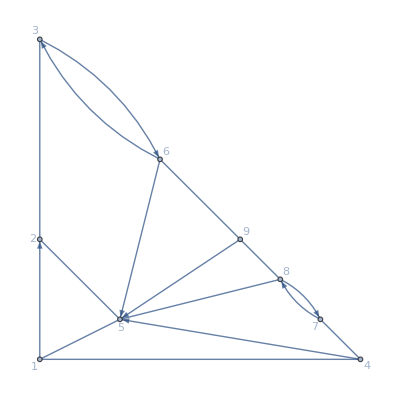

```mathematica
boardGraph=Graph[{1,2,3,6,9,5,4,7,8},{DirectedEdge[1,2],UndirectedEdge[2,3],DirectedEdge[3,6],DirectedEdge[6,3],UndirectedEdge[6,9],UndirectedEdge[1,5],UndirectedEdge[2,5],DirectedEdge[6,5],UndirectedEdge[1,4],DirectedEdge[4,5],UndirectedEdge[7,4],DirectedEdge[7,8],DirectedEdge[8,7],UndirectedEdge[5,8],UndirectedEdge[8,9],DirectedEdge[9,5]},{GraphLayout->"PlanarEmbedding",VertexLabels->{Automatic}}]
```

### Examples

#### A^+(S) arcs leaving S

```mathematica
APlus[boardGraph,{2,3,5}]
```

{3->6}

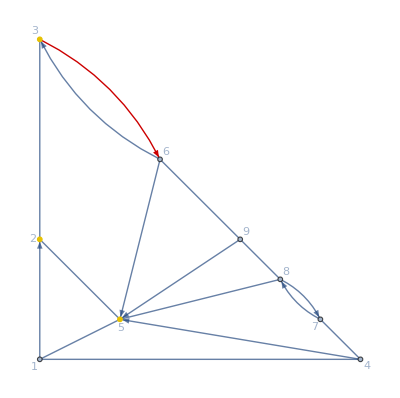

```mathematica
HighlightGraph[boardGraph,{APlus[boardGraph,{2,3,5}],{2,3,5}}]
```

#### D^+(S) # of arcs leaving S

```mathematica
DPlus//ClearAll
DPlus[graph_?GraphQ,set_]:=Length[Cases[IncidenceList[graph,Alternatives@@set],Alternatives@@set->Except[Alternatives@@set]]]
```

#### A^-(S) arcs entering S

```mathematica
AMinus[boardGraph,{2,3,5}]
```

{1->2,6->3,6->5,4->5,9->5}

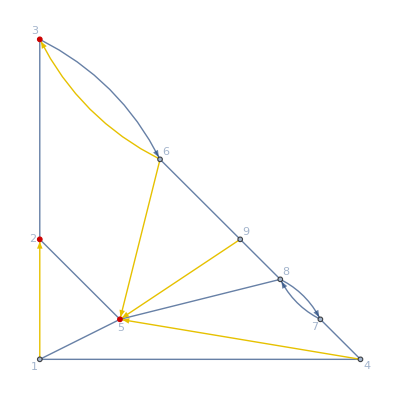

```mathematica
HighlightGraph[boardGraph,{{2,3,5},AMinus[boardGraph,{2,3,5}]}]
```

#### D^-(S) # of arcs leaving S

```mathematica
DMinus[boardGraph,{2,3,5}]
```

5

#### E(S) edges incident with S

```mathematica
EOfS[boardGraph,{2,3,5}]
```

{1<->5,5<->8}

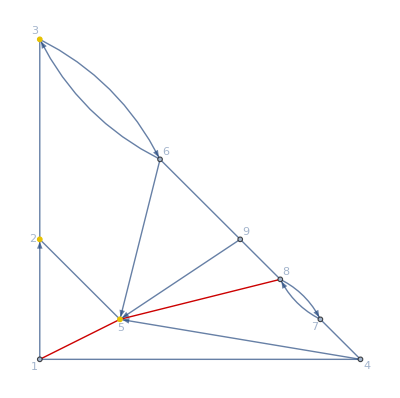

```mathematica
HighlightGraph[boardGraph,{EOfS[boardGraph,{2,3,5}],{2,3,5}}]
```

#### D(S) # of edges incident with S

```mathematica
DOfEOfS[boardGraph,{2,3,5}]
```

2

#### A(S) arcs entering or leaving S

```mathematica
AOfS[boardGraph,{2,3,5}]
```

{1->2,3->6,6->3,6->5,4->5,9->5}

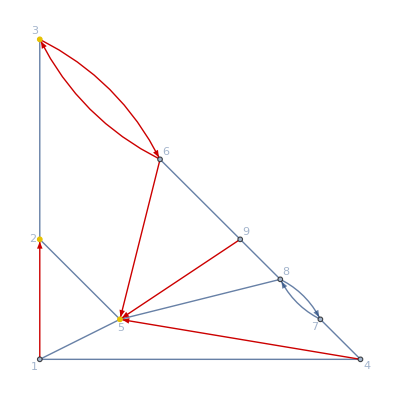

```mathematica
HighlightGraph[boardGraph,{AOfS[boardGraph,{2,3,5}],{2,3,5}}]
```

#### All arcs in the graph

```mathematica
ArcList[boardGraph]
```

{1->2,3->6,6->3,6->5,4->5,7->8,8->7,9->5}

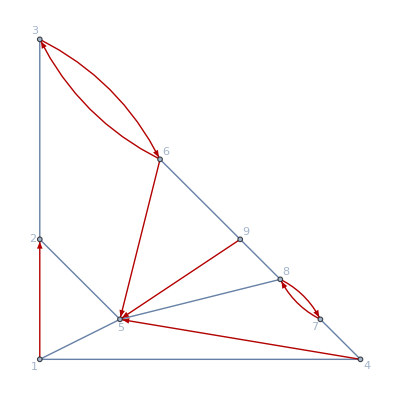

```mathematica
HighlightGraph[boardGraph,ArcList[boardGraph]]
```

#### # of arcs in the graph

```mathematica
ArcCount[boardGraph]
```

8

#### All undirected edges

```mathematica
EList[boardGraph]
```

{2<->3,6<->9,1<->5,2<->5,1<->4,7<->4,5<->8,8<->9}

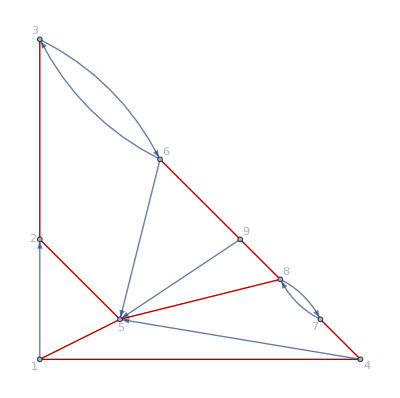

```mathematica
HighlightGraph[boardGraph,EList[boardGraph]]
```

#### # of undirected edges

```mathematica
DOfEList[boardGraph]
```

8

### Optimum Variables

Let x_(i,j) and y_(i,j) represent, respectively, the optimal numbers of copies of arc (i,j)∈A and edge (i,j)∈E which added to graph G, make it Eulerian. Define the graph G_(x,y) as the original graph with the additional copies of links indicated by the values of x_(i,j) and y_(i,j). More precisely, if x_(i,j)=p, then G_(x,y) will contain (p+1) arcs (i,j). A similar interpretation is given to y_(i,j)=p. Graphs G_(x,y) with (x,y) fractional will be considered. We comment after on this.

```mathematica
EdgeList[boardGraph]
```

{1->2,2<->3,3->6,6->3,6<->9,1<->5,2<->5,6->5,1<->4,4->5,7<->4,7->8,8->7,5<->8,8<->9,9->5}

```mathematica
EdgeList[boardGraph]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}
```

{x12,y23,x36,x63,y69,y15,y25,x65,y14,x45,y74,x78,x87,y58,y89,x95}

```mathematica
OptimumCopiesArray//ClearAll
OptimumCopiesArray[graph_?GraphQ]:=EdgeList[graph]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}
```

```mathematica
TotalOptimumCopies//ClearAll
TotalOptimumCopies[graph_?GraphQ]:=Total[EdgeList[graph]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]
```

```mathematica
TotalOptimumCopies[boardGraph]
```

x12+x36+x45+x63+x65+x78+x87+x95+y14+y15+y23+y25+y58+y69+y74+y89

```mathematica
OptimumCopiesArray[boardGraph]
```

{x12,y23,x36,x63,y69,y15,y25,x65,y14,x45,y74,x78,x87,y58,y89,x95}

```mathematica
StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"<->","variable"->"y","first"->1,"last"->2|>]
```

The total number of times the edge 1<->2 is replaced is given by y_(1, 2).

```mathematica
StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"->","variable"->"x","first"->1,"last"->2|>]
```

The total number of times the edge 1->2 is replaced is given by x_(1, 2).

```mathematica
UndirectedEdgeOptimumVariable//ClearAll
UndirectedEdgeOptimumVariable[edge_]:=StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"<->","variable"->"y","first"->First[edge],"last"->Last[edge]|>]
```

```mathematica
UndirectedEdgeOptimumVariable/@EList[boardGraph]
```

{The total number of times the edge 2<->3 is replaced is given by y_(2, 3).,The total number of times the edge 6<->9 is replaced is given by y_(6, 9).,The total number of times the edge 1<->5 is replaced is given by y_(1, 5).,The total number of times the edge 2<->5 is replaced is given by y_(2, 5).,The total number of times the edge 1<->4 is replaced is given by y_(1, 4).,The total number of times the edge 7<->4 is replaced is given by y_(7, 4).,The total number of times the edge 5<->8 is replaced is given by y_(5, 8).,The total number of times the edge 8<->9 is replaced is given by y_(8, 9).}

```mathematica
UndirectedEdgeOptimumVariableKeyMap//ClearAll
UndirectedEdgeOptimumVariableKeyMap[graph_?GraphQ]:=AssociationMap[Function[edge,StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"<->","variable"->"y","first"->First[edge],"last"->Last[edge]|>]],EdgeList[graph,_<->_]]
```

```mathematica
UndirectedEdgeOptimumVariableKeyMap[boardGraph][2<->3]
```

The total number of times the edge 2<->3 is replaced is given by y_(2, 3).

```mathematica
DirectedEdgeOptimumVariableKeyMap//ClearAll
DirectedEdgeOptimumVariableKeyMap[graph_?GraphQ]:=AssociationMap[Function[edge,StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"->","variable"->"x","first"->First[edge],"last"->Last[edge]|>]],EdgeList[graph,_->_]]
```

```mathematica
DirectedEdgeOptimumVariableKeyMap[boardGraph]
```

<|1->2→The total number of times the edge 1->2 is replaced is given by y_(1, 2).,3->6→The total number of times the edge 3->6 is replaced is given by y_(3, 6).,6->3→The total number of times the edge 6->3 is replaced is given by y_(6, 3).,6->5→The total number of times the edge 6->5 is replaced is given by y_(6, 5).,4->5→The total number of times the edge 4->5 is replaced is given by y_(4, 5).,7->8→The total number of times the edge 7->8 is replaced is given by y_(7, 8).,8->7→The total number of times the edge 8->7 is replaced is given by y_(8, 7).,9->5→The total number of times the edge 9->5 is replaced is given by y_(9, 5).|>

```mathematica
OptimumCopiesKeyMap[graph_?GraphQ]:=Join[AssociationMap[Function[edge,StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"->","variable"->"x","first"->First[edge],"last"->Last[edge]|>]],EdgeList[graph,_->_]],AssociationMap[Function[edge,StringTemplate["The total number of times the edge `first``directedorundirected``last` is replaced is given by (`variable`)_(`first`, `last`)."][<|"directedorundirected"->"<->","variable"->"y","first"->First[edge],"last"->Last[edge]|>]],EdgeList[graph,_<->_]]]
```

```mathematica
OptimumCopiesKeyMap[boardGraph]
```

<|1->2→The total number of times the edge 1->2 is replaced is given by x_(1, 2).,3->6→The total number of times the edge 3->6 is replaced is given by x_(3, 6).,6->3→The total number of times the edge 6->3 is replaced is given by x_(6, 3).,6->5→The total number of times the edge 6->5 is replaced is given by x_(6, 5).,4->5→The total number of times the edge 4->5 is replaced is given by x_(4, 5).,7->8→The total number of times the edge 7->8 is replaced is given by x_(7, 8).,8->7→The total number of times the edge 8->7 is replaced is given by x_(8, 7).,9->5→The total number of times the edge 9->5 is replaced is given by x_(9, 5).,2<->3→The total number of times the edge 2<->3 is replaced is given by y_(2, 3).,6<->9→The total number of times the edge 6<->9 is replaced is given by y_(6, 9).,1<->5→The total number of times the edge 1<->5 is replaced is given by y_(1, 5).,2<->5→The total number of times the edge 2<->5 is replaced is given by y_(2, 5).,1<->4→The total number of times the edge 1<->4 is replaced is given by y_(1, 4).,7<->4→The total number of times the edge 7<->4 is replaced is given by y_(7, 4).,5<->8→The total number of times the edge 5<->8 is replaced is given by y_(5, 8).,8<->9→The total number of times the edge 8<->9 is replaced is given by y_(8, 9).|>

```mathematica
?OptimumCopiesArray
```

```mathematica
GraphWeightConstantArray//ClearAll
GraphWeightConstantArray[graph_?GraphQ]:=EdgeList[graph]/.{u_->v_:>cuv,u_<->v_:>duv}
```

```mathematica
GraphWeightConstantArray[boardGraph]
```

{c12,d23,c36,c63,d69,d15,d25,c65,d14,c45,d74,c78,c87,d58,d89,c95}

```mathematica
GraphWeightConstantArray[boardGraph].OptimumCopiesArray[boardGraph]
```

c12 x12+c36 x36+c45 x45+c63 x63+c65 x65+c78 x78+c87 x87+c95 x95+d14 y14+d15 y15+d23 y23+d25 y25+d58 y58+d69 y69+d74 y74+d89 y89

```mathematica
GraphMinimizationObjectiveExpression//ClearAll
GraphMinimizationObjectiveExpression[graph_?GraphQ]:=(EdgeList[graph]/.{u_->v_:>cuv,u_<->v_:>duv}).(EdgeList[graph]/.{u_->v_:>xuv,u_<->v_:>yuv})
```

```mathematica
GraphMinimizationObjectiveExpression[boardGraph]
```

c12 x12+c36 x36+c45 x45+c63 x63+c65 x65+c78 x78+c87 x87+c95 x95+d14 y14+d15 y15+d23 y23+d25 y25+d58 y58+d69 y69+d74 y74+d89 y89

```mathematica
OptimumArcCopiesArray//ClearAll
OptimumArcCopiesArray[graph_?GraphQ]:=EdgeList[graph,_->_]/.{u_->v_:>xuv,u_<->v_:>yuv}
```

```mathematica
Total[OptimumCopiesArray[boardGraph]]
```

x12+x36+x45+x63+x65+x78+x87+x95+y14+y15+y23+y25+y58+y69+y74+y89

```mathematica
PVariableOddOrEven//ClearAll
PVariableOddOrEven[graph_?GraphQ,node_]:=Boole[OddQ[VertexDegree[graph,node]]]
```

```mathematica
PVariableOddOrEven[boardGraph,1]
```

1

```mathematica
PVariableOddOrEven[boardGraph,8]
```

0

```mathematica
EvenCondition2//ClearAll
EvenCondition2[graph_?GraphQ]:=Total[OptimumCopiesArray[boardGraph]]==2v
```

```mathematica
Union[AOfS[boardGraph,{1}],EOfS[boardGraph,{1}]]
```

{1->2,1<->4,1<->5}

```mathematica
Union[AOfS[boardGraph,{1}],EOfS[boardGraph,{1}]]/.{u_->v_:>xuv,u_<->v_:>yuv}
```

{x12,y14,y15}

```mathematica
Total[Union[AOfS[boardGraph,{1}],EOfS[boardGraph,{1}]]/.{u_->v_:>xuv,u_<->v_:>yuv}]
```

x12+y14+y15

```mathematica
EvenCondition2OfS//ClearAll
EvenCondition2OfS[graph_?GraphQ,node_]:=((Total[Union[AOfS[graph,{node}],EOfS[graph,{node}]]/.{u_->v_:>xuv,u_<->v_:>yuv}])==2Indexed[v,node]+PVariableOddOrEven[graph,node])/;MemberQ[VertexList[graph],node]
```

```mathematica
EvenCondition2OfS[boardGraph,1]
```

x12+y14+y15==1+2 v1

```mathematica
AllEvenConditions2//ClearAll
AllEvenConditions2[graph_?GraphQ]:=Map[Function[node,((Total[Union[AOfS[graph,{node}],EOfS[graph,{node}]]/.{u_->v_:>xuv,u_<->v_:>yuv}])==2Indexed[v,node]+PVariableOddOrEven[graph,node])],VertexList[graph]]
```

```mathematica
AllEvenConditions2[boardGraph]
```

{x12+y14+y15==1+2 v1,x12+y23+y25==1+2 v2,x36+x63+y23==1+2 v3,x36+x63+x65+y69==2 v6,x95+y69+y89==1+2 v9,x45+x65+x95+y15+y25+y58==2 v5,x45+y14+y74==1+2 v4,x78+x87+y74==1+2 v7,x78+x87+y58+y89==2 v8}

```mathematica
BalancedSetCondition//ClearAll
BalancedSetCondition[graph_?GraphQ]:=
```

```mathematica
APlus[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}
```

{x12,x45,x78}

```mathematica
Total[APlus[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]
```

x12+x45+x78

```mathematica
Total[AMinus[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]
```

x87

```mathematica
Total[EOfS[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]
```

y15

```mathematica
-Total[APlus[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]+Total[AMinus[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]+Total[EOfS[boardGraph,{1,4,7}]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]>=(DPlus[boardGraph,{1,4,7}]-DMinus[boardGraph,{1,4,7}]-DOfEOfS[boardGraph,{1,4,7}])
```

-x12-x45-x78+x87+y15≥1

```mathematica
BalancedSetCondition//ClearAll
BalancedSetCondition[graph_?GraphQ,set_]:=-Total[APlus[graph,set]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]+Total[AMinus[graph,set]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]+Total[EOfS[graph,set]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]>=(DPlus[graph,set]-DMinus[graph,set]-DOfEOfS[graph,set])
```

```mathematica
BalancedSetCondition[boardGraph,{1,4,7}]
```

-x12-x45-x78+x87+y15≥1

```mathematica
AllBalancedSetConditions//ClearAll
AllBalancedSetConditions[graph_?GraphQ]:=BalancedSetCondition[graph,#]&/@Subsets[VertexList[graph]]
```

```mathematica
AllBalancedSetConditions[boardGraph]
```

```mathematica
Reduce[And@@AllBalancedSetConditions[boardGraph]]
```

$Aborted

```mathematica
BalancedSetConditionWithoutInequality//ClearAll
BalancedSetConditionWithoutInequality[graph_?GraphQ,set_]:=-Total[APlus[graph,set]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]+Total[AMinus[graph,set]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]+Total[EOfS[graph,set]/.{u_->v_:>Indexed[x,{u,v}],u_<->v_:>Indexed[y,{u,v}]}]
```

```mathematica
BalancedSetConditionWithoutInequality[boardGraph,{1,4,7}]
```

-x12-x45-x78+x87+y15

```mathematica
AllBalancedSetConditionsWithoutInequalities//ClearAll
AllBalancedSetConditionsWithoutInequalities[graph_?GraphQ]:=BalancedSetConditionWithoutInequality[graph,#]&/@Subsets[VertexList[graph]]
```

```mathematica
AllBalancedSetConditionsWithoutInequalities[boardGraph]
```

```mathematica
DeleteCases[AllBalancedSetConditionsWithoutInequalities[boardGraph],0]
```

```mathematica
GroebnerBasis[DeleteCases[AllBalancedSetConditionsWithoutInequalities[boardGraph],0],]
```

{x78-x87,y74,y58,x45,y89,x95,y69,x65,x36-x63,y25,y23,y15,y14,x12}

```mathematica
OptimumCopiesArray[boardGraph]
```

{x12,y23,x36,x63,y69,y15,y25,x65,y14,x45,y74,x78,x87,y58,y89,x95}

```mathematica
GroebnerBasis[DeleteCases[AllBalancedSetConditionsWithoutInequalities[boardGraph],0],OptimumCopiesArray[boardGraph]]
```

{x95,y89,y58,x78-x87,y74,x45,y14,x65,y25,y15,y69,x36-x63,y23,x12}

```mathematica
IncidenceList[boardGraph,9|5]
```

{6<->9,1<->5,2<->5,6->5,4->5,5<->8,8<->9,9->5}

```mathematica
BalancedSetCondition[boardGraph,#]&/@IncidenceList[boardGraph,9|5]
```

{x36-x63-x65-x95+y89≥1,-x12+x45+x65+x95+y14+y25+y58≥-5,x12+x45+x65+x95+y15+y23+y58≥-7,x36+x45-x63+x95+y15+y25+y58+y69≥-6,x65+x95+y14+y15+y25+y58+y74≥-7,x45+x65+x78-x87+x95+y15+y25+y89≥-6,x78-x87-x95+y58+y69≥-1,x45+x65+y15+y25+y58+y69+y89≥-7}

```mathematica
Last[Indexed[x,{3,4}]]
```

{3,4}

```mathematica
If[First[Indexed[x,{3,4}]]==x,First[Last[Indexed[x,{3,4}]]]->Last[Last[Indexed[x,{3,4}]]]]
```

3->4

```mathematica
If[First[Indexed[x,{3,4}]]==x,First[Last[Indexed[x,{3,4}]]]->Last[Last[Indexed[x,{3,4}]]],First[Last[Indexed[x,{3,4}]]]<->Last[Last[Indexed[x,{3,4}]]]]
```

3->4

```mathematica
ConvertVariableToEdge[variable_]:=Block[{first,last},first=First[Last[variable]];
last=Last[Last[variable]];
If[MatchQ[First[variable],x],First[Last[variable]]->Last[Last[variable]],If[MatchQ[First[variable],y],First[Last[variable]]<->Last[Last[variable]]]]]
```

```mathematica
ConvertVariableToEdge[x95]
```

9->5

```mathematica
ConvertVariableToEdge[y95]
```

9<->5

```mathematica
ConvertVariableToEdge/@GroebnerBasis[DeleteCases[AllBalancedSetConditionsWithoutInequalities[boardGraph],0],OptimumCopiesArray[boardGraph]]
```

{9->5,8<->9,5<->8,Null,7<->4,4->5,1<->4,6->5,2<->5,1<->5,6<->9,Null,2<->3,1->2}

```mathematica
Level[x-b,1]
```

{-b,x}

```mathematica
FindMaximumFlow[boardGraph,1,2,"VertexList"]
```

{1,2,3,6,9,5,4,7,8}

```mathematica
FindMaximumFlow[boardGraph,1,3,"VertexList"]
```

{1,2,3,6,9,5,4,7,8}

```mathematica
DeleteCases[{u_,u_}][Tuples[Range[9],2]]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,1},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,1},{3,2},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,1},{4,2},{4,3},{4,5},{4,6},{4,7},{4,8},{4,9},{5,1},{5,2},{5,3},{5,4},{5,6},{5,7},{5,8},{5,9},{6,1},{6,2},{6,3},{6,4},{6,5},{6,7},{6,8},{6,9},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,8},{7,9},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,9},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8}}

```mathematica
FindMaximumFlow[boardGraph,#1,#2,"VertexList"]&@@@DeleteCases[{u_,u_}][Tuples[Range[9],2]]//Short
```

{{1,2,3,6,9,5,4,7,8},«70»,{1,2,3,6,9,5,4,7,8}}

```mathematica
FindMaximumFlow[boardGraph,{1,2,3},{4,5,6}]
```

4

```mathematica
FindMaximumFlow[boardGraph,{1,2,3},{4,5,6},"OptimumFlowData"]
```

OptimumFlowData[…]

```mathematica
FindMaximumFlow[boardGraph,{1,2,3},{4,5,6},"OptimumFlowData"]["Properties"]
```

{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList}

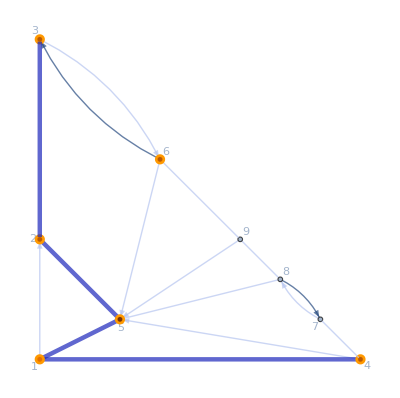
{4,{1<->2,1<->5,1<->4,2<->3,2<->5,3<->6},-Graphics-,SparseArray[…],OptimumFlowData[…][FlowTable],4,{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList},OptimumFlowData[…][ResidualGraph],{1,2,3,6,9,5,4,7,8}}

```mathematica
FindMaximumFlow[boardGraph,{1,2,3},{4,5,6},"OptimumFlowData"][#]&/@FindMaximumFlow[boardGraph,{1,2,3},{4,5,6},"OptimumFlowData"]["Properties"]
```

## Windy Postman Cutting Equatilities